```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
dr9Data=Import["exports/location.dr9.csv"];
dr7Data=Import["exports/location.dr7.csv"];
matchData=Import["exports/match.csv"];
```

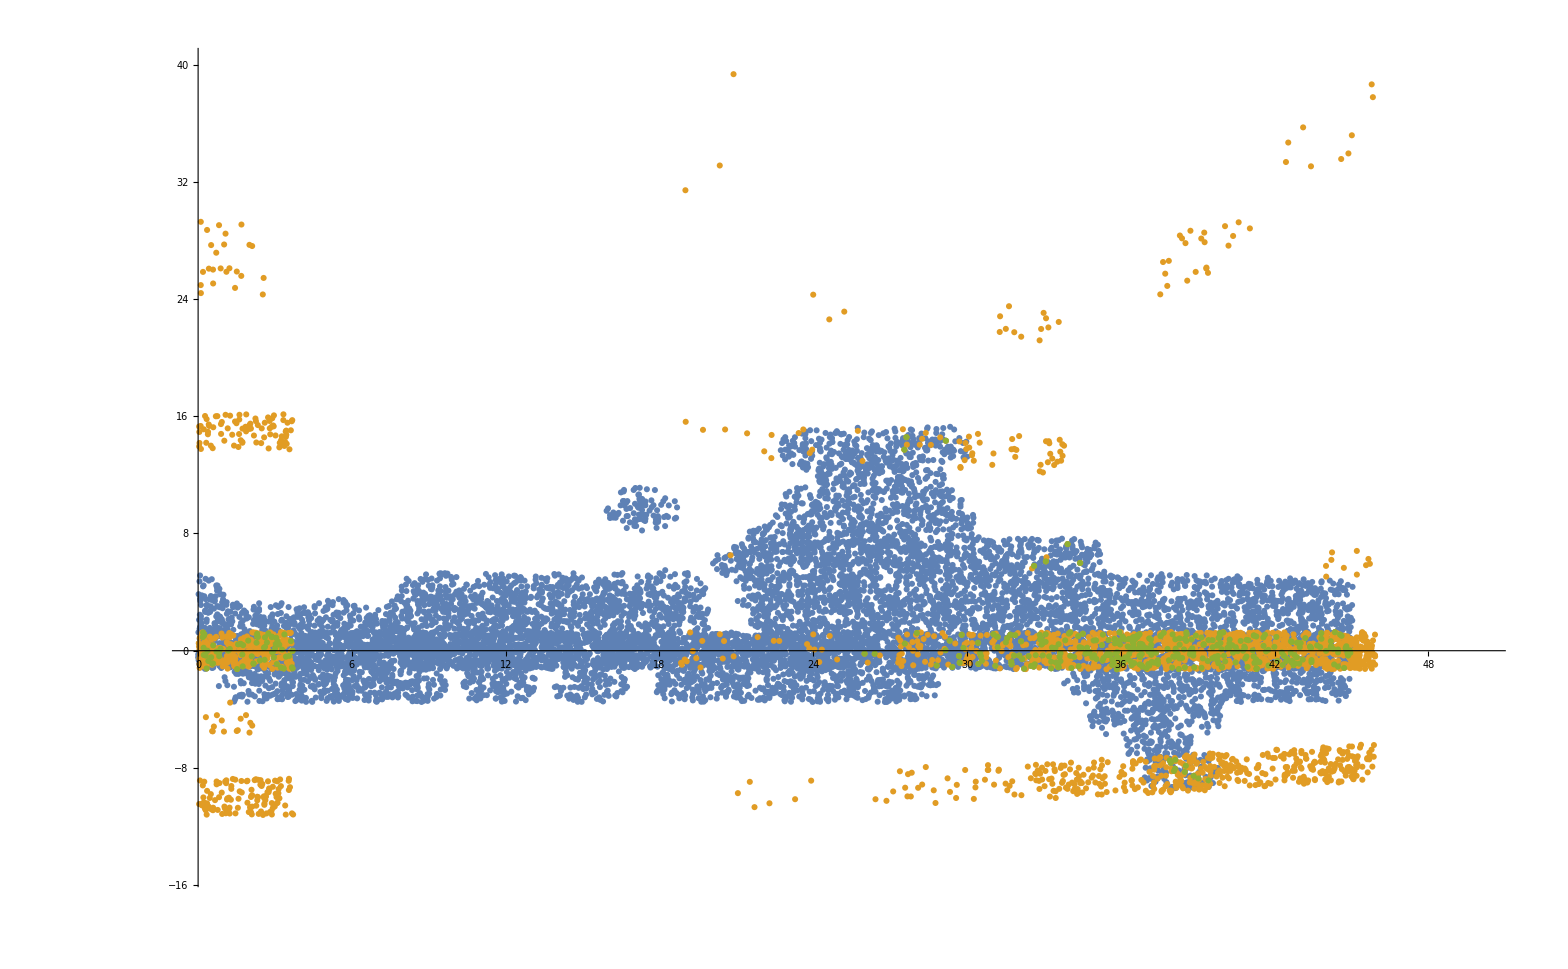

```mathematica
ListPlot[
{
dr9Data[[All,{1,2}]],
dr7Data[[All,{1,2}]],
matchData[[All, {1,2}]]
},
PlotRange->{{0,50},{-15,40}}
]
```

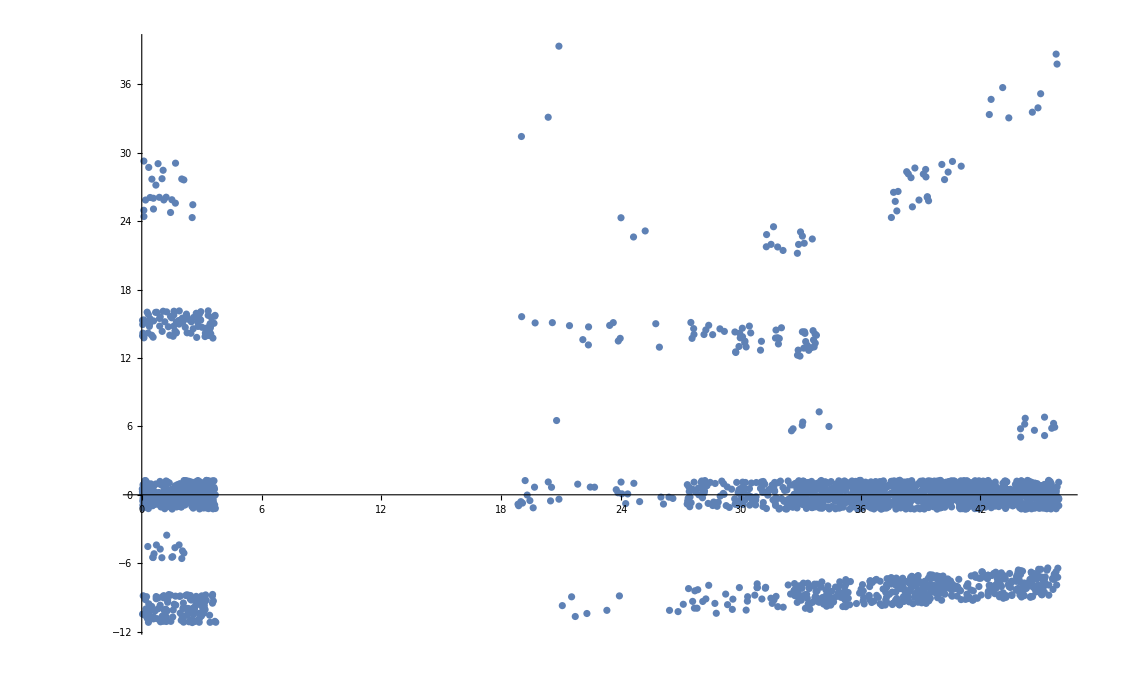

```mathematica
ListPlot[
{
dr7Data[[All,{1,2}]]
},
PlotRange->{All, All}
]
```

```mathematica
Image[
Partition[
dr9Data[[All,{1,2,3}]],
256]
]
```

-Graphics-

```mathematica
Image[
Partition[
dr7Data[[All,{1,2,3}]],
256]
]
```

-Graphics-